```mathematica
SetDirectory["C:\\Users\\Georg\\Desktop\\figs"];
<<"CustomTicks.m"
```

```mathematica
ϵ=.
μ=.
Ω=.
u=.
i0=Integrate[(-μ/(-1+u (ϵ μ+λ)-Ω)+(1+ϵ)μ/(1+u (ϵ μ+λ)-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals&&λ>0]
i1=Integrate[u(-μ/(-1+u (ϵ μ+λ)-Ω)+(1+ϵ)μ/(1+u (ϵ μ+λ)-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals&&λ>0]
i2=Integrate[u^2(-μ/(-1+u (ϵ μ+λ)-Ω)+(1+ϵ)μ/(1+u (ϵ μ+λ)-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals&&λ>0]
```

(μ ((1+ϵ) Log[(1+λ+ϵ μ-Ω)/(1-Ω)]-Log[(1-λ-ϵ μ+Ω)/(1+Ω)]))/(λ+ϵ μ)

(μ (ϵ λ+ϵ^2 μ-(1+ϵ) (-1+Ω) Log[1-Ω]+(1+ϵ) (-1+Ω) Log[1+λ+ϵ μ-Ω]+Log[1+Ω]+Ω Log[1+Ω]-Log[1-λ-ϵ μ+Ω]-Ω Log[1-λ-ϵ μ+Ω]))/(λ+ϵ μ)^2

1/(2 (λ+ϵ μ)^3)μ (-4 λ-2 ϵ λ+ϵ λ^2-4 ϵ μ-2 ϵ^2 μ+2 ϵ^2 λ μ+ϵ^3 μ^2+2 ϵ λ Ω+2 ϵ^2 μ Ω-2 (1+ϵ) (-1+Ω)^2 Log[1-Ω]+2 (1+ϵ) (-1+Ω)^2 Log[1+λ+ϵ μ-Ω]+2 Log[1+Ω]+4 Ω Log[1+Ω]+2 Ω^2 Log[1+Ω]-2 Log[1-λ-ϵ μ+Ω]-4 Ω Log[1-λ-ϵ μ+Ω]-2 Ω^2 Log[1-λ-ϵ μ+Ω])

```mathematica
h=.
FullSimplify[(h-i1)^2,Assumptions->μ∈Reals&&ϵ>0&&Ω∉Reals&&h∈Reals&&λ>0]
```

((λ+ϵ μ) (h λ+(-1+h) ϵ μ)-μ (2 Ω ArcTanh[Ω]+(1+ϵ-ϵ Ω) Log[1-Ω]+(1+ϵ) (-1+Ω) Log[1+λ+ϵ μ-Ω]+Log[1+Ω])+μ (1+Ω) Log[1-λ-ϵ μ+Ω])^2/(λ+ϵ μ)^4

```mathematica
FullSimplify[-i0 i2,Assumptions->μ∈Reals&&ϵ>0&&Ω∉Reals&&h∈Reals&&λ>0]
```

-1/(2 (λ+ϵ μ)^4)μ^2 ((λ+ϵ μ) (-4+ϵ (-2+λ+ϵ μ+2 Ω))-2 (1+ϵ) (-1+Ω)^2 Log[1-Ω]+2 (1+ϵ) (-1+Ω)^2 Log[1+λ+ϵ μ-Ω]+2 (1+Ω)^2 Log[1+Ω]-2 Log[1-λ-ϵ μ+Ω]-2 Ω (2+Ω) Log[1-λ-ϵ μ+Ω]) ((1+ϵ) Log[(1+λ+ϵ μ-Ω)/(1-Ω)]-Log[(1-λ-ϵ μ+Ω)/(1+Ω)])

```mathematica
d[h_,ϵ_,μ_,λ_,Ω_]:=1/(λ+ϵ μ)^4((λ+ϵ μ) (h λ+(-1+h) ϵ μ)-μ (2 Ω ArcTanh[Ω]+(1+ϵ-ϵ Ω) Log[1-Ω]+(1+ϵ) (-1+Ω) Log[1+λ+ϵ μ-Ω]+Log[1+Ω])+μ (1+Ω) Log[1-λ-ϵ μ+Ω])^2-1/(2 (λ+ϵ μ)^4)μ^2 ((λ+ϵ μ) (-4+ϵ (-2+λ+ϵ μ+2 Ω))+4 (1+Ω^2) ArcTanh[Ω]-2 (ϵ (-1+Ω)^2-2 Ω) Log[1-Ω]-2 Log[1-λ-ϵ μ+Ω]+2 ((1+ϵ) (-1+Ω)^2 Log[1+λ+ϵ μ-Ω]+2 Ω Log[1+Ω]-Ω (2+Ω) Log[1-λ-ϵ μ+Ω])) ((1+ϵ) Log[(1+λ+ϵ μ-Ω)/(1-Ω)]-Log[(1-λ-ϵ μ+Ω)/(1+Ω)])
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot :: cvmit will be suppressed during this calculation.

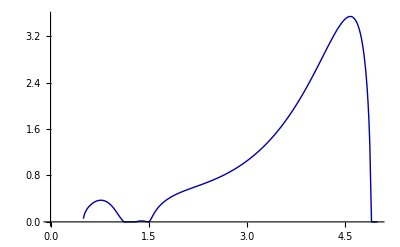

```mathematica
λ=0.;
Ω0=1.+0.2I;
k[μ_]:=Module[{m=μ,Ω},Ω0=Last[Last[FindRoot[d[-1,0.5,m,λ,Ω]==0,{Ω,Ω0+0.01I}]]];Abs[Im[Ω0]]]
t1=Table[{a,k[10^a]},{a,5.0,0.5,-0.013}];
f1=ListLinePlot[t1,PlotStyle->{Darker[Blue],Thick}]
```

```mathematica
λ=0;
ϵ=1/2;
μ=40000.;
h=-1;
Ω0=10.+0.5 I
Ω=Last[Last[FindRoot[d[h,ϵ,μ,λ,W]==0,{W,Ω0+0.01I}]]]
i0=Integrate[(-μ/(-1+u (ϵ μ+λ)-Ω)+(1+ϵ)μ/(1+u (ϵ μ+λ)-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals&&λ∈Reals];
i1=Integrate[u(-μ/(-1+u (ϵ μ+λ)-Ω)+(1+ϵ)μ/(1+u (ϵ μ+λ)-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals&&λ∈Reals];
i2=Integrate[u^2(-μ/(-1+u (ϵ μ+λ)-Ω)+(1+ϵ)μ/(1+u (ϵ μ+λ)-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals&&λ∈Reals];
(i1-h)^2-i0 i2;
b=1;
a=Last[Last[Last[Solve[(i1-h)aa+i2 b==0,aa]]]];
ω=0;
Q[ω_,u_]:=(a+b u)/(ω+(ϵ μ+λ)u-Ω)
ω=0;
rx=.
ry=.
eq1=(Re[Q[ω,0]]-rx)^2+(Im[Q[ω,0]]-ry)^2==(Re[Q[ω,1/2]]-rx)^2+(Im[Q[ω,1/2]]-ry)^2;
eq2=(Re[Q[ω,1]]-rx)^2+(Im[Q[ω,1]]-ry)^2==(Re[Q[ω,1/2]]-rx)^2+(Im[Q[ω,1/2]]-ry)^2;
ss=Solve[{eq1,eq2},{rx, ry}];
rx=Last[First[Last[ss]]];
ry=Last[Last[Last[ss]]];
p=(rx - I ry)/(rx^2+ry^2);
ω=.
Clear[Q]
Q[ω_,u_]:=p(a+b u)/(ω+(ϵ μ+λ)u-Ω)
```

10.+0.5 ⅈ

-1.72464+3.53921 ⅈ

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
Q[1,u]//FullSimplify
```

(6.92343×10^-7+0.00141415 ⅈ)-(0.0100107+7.07982 ⅈ)/((2.72464-3.53921 ⅈ)+20000. u)

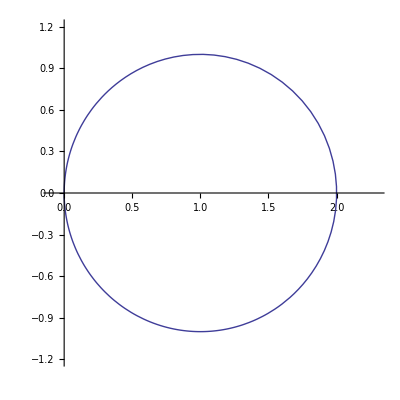

```mathematica
ParametricPlot[{{Re[Q[1,x^3]],Im[Q[1,x^3]]}},{x,-1,2},PlotRange->{{-0.1,2.3},{-1.2,1.2}},AspectRatio->1]
```

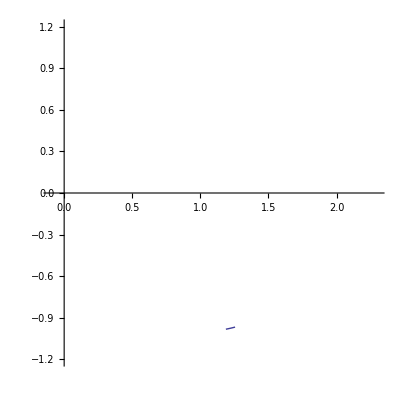

```mathematica
ParametricPlot[{{Re[Q[1,u]],Im[Q[1,u]]}},{u,0,0.00001},PlotRange->{{-0.1,2.3},{-1.2,1.2}},AspectRatio->1]
```

```mathematica
ParametricPlot[{{Re[Q[1,x^3]],Im[Q[1,x^3]]},{Re[Q[-1,x^3]],Im[Q[-1,x^3]]}},{x,-10,10},PlotRange->{{-0.1,2.3},{-1.2,1.2}},AspectRatio->1]
```

```mathematica
t1={{Re[Q[1,0]],Im[Q[1,0]]},{Re[Q[1,0.0001]],Im[Q[1,0.0001]]},{Re[Q[1,0.001]],Im[Q[1,0.001]]},{Re[Q[1,0.01]],Im[Q[1,0.01]]}}
```

{{1.25464,-0.967294},{0.717676,-0.959469},{0.046943,-0.302823},{0.000560839,-0.0334994}}

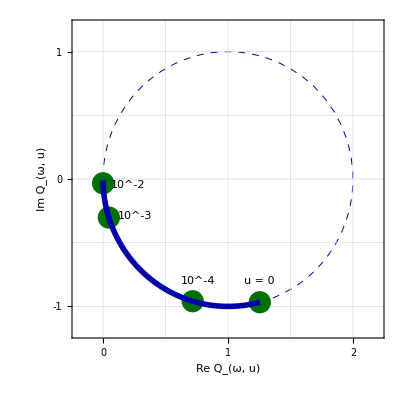

vec3.eps

```mathematica
p1=ParametricPlot[{Re[Q[1,x^3]],Im[Q[1,x^3]]},{x,-2,2},PlotRange->{{-0.2,2.2},{-1.2,1.2}},AspectRatio->1,
ImageSize->{400,400},ImagePadding->{{80,20},{80,20}},
PlotStyle->{{AbsoluteThickness[0.7],Darker[Blue],Dashed},{AbsoluteThickness[0.7],Darker[Red],Dashed},{AbsoluteThickness[0.5],Black}},
BaseStyle->{FontFamily->"Helvetica",14},Frame->True,Axes->False,GridLines->{{0,0.5,1,1.5,2},{-1,-0.5,0,0.5,1}},
Epilog-> {Inset["u = 0",{1.25,-0.8},{Center,Center}],Inset["10^-4",{0.76,-0.8},{Center,Center}],Inset["10^-3",{0.26,-0.29},{Center,Center}],Inset["10^-2",{0.2,-0.05},{Center,Center}]},
FrameStyle->AbsoluteThickness[0.7],FrameLabel->{Style["Re Q_(ω, u)",14],Style["Im Q_(ω, u)",14]},
FrameTicks->{LinTicks[-1,3,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-1,3,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[-2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}];
p2=ParametricPlot[{{Re[Q[1,u]],Im[Q[1,u]]}},{u,0,.03},AspectRatio->1,Axes->False,
PlotStyle->{{AbsoluteThickness[4],Darker[Blue]},{AbsoluteThickness[4],Darker[Red]}}];
p3=ListPlot[t1,AspectRatio->1,Axes->False,
PlotStyle->{{PointSize[0.04],Darker[Darker[Green]]}}];
plot1=Show[p1,p3,p2]
Export["vec3.eps",plot1]
```

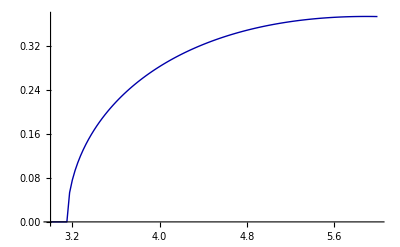

1.0393+0.373122 ⅈ

```mathematica
λ=0.;
Ω0=1.+0.2I;
k[μ_]:=Module[{m=μ,Ω},Ω0=Last[Last[FindRoot[d[-1,0.5,m,λ,Ω]==0,{Ω,Ω0+0.01I}]]];Abs[Im[Ω0]]]
t1=Table[{m,k[m]},{m,3,6,0.025}];
f1=ListLinePlot[t1,PlotStyle->{Darker[Blue],Thick}]
Ω0
```

```mathematica
Ω=Ω0
μ=6.
i0=Integrate[(-μ/(-1+u (ϵ μ+λ)-Ω)+(1+ϵ)μ/(1+u (ϵ μ+λ)-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals&&λ∈Reals];
i1=Integrate[u(-μ/(-1+u (ϵ μ+λ)-Ω)+(1+ϵ)μ/(1+u (ϵ μ+λ)-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals&&λ∈Reals];
i2=Integrate[u^2(-μ/(-1+u (ϵ μ+λ)-Ω)+(1+ϵ)μ/(1+u (ϵ μ+λ)-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals&&λ∈Reals];
(i1-h)^2-i0 i2;
b=1;
a=Last[Last[Last[Solve[(i1-h)aa+i2 b==0,aa]]]];
ω=0;
Q[ω_,u_]:=(a+b u)/(ω+(ϵ μ+λ)u-Ω)
ω=0;
rx=.
ry=.
eq1=(Re[Q[ω,0]]-rx)^2+(Im[Q[ω,0]]-ry)^2==(Re[Q[ω,1/2]]-rx)^2+(Im[Q[ω,1/2]]-ry)^2;
eq2=(Re[Q[ω,1]]-rx)^2+(Im[Q[ω,1]]-ry)^2==(Re[Q[ω,1/2]]-rx)^2+(Im[Q[ω,1/2]]-ry)^2;
ss=Solve[{eq1,eq2},{rx, ry}];
rx=Last[First[Last[ss]]];
ry=Last[Last[Last[ss]]];
p=(rx - I ry)/(rx^2+ry^2);
ω=.
Clear[Q]
Q[ω_,u_]:=p(a+b u)/(ω+(ϵ μ+λ)u-Ω)
```

1.0393+0.373122 ⅈ

6.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

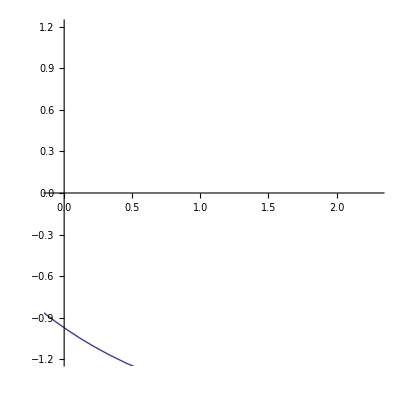

```mathematica
ParametricPlot[{{Re[Q[1,u]],Im[Q[1,u]]}},{u,0,1},PlotRange->{{-0.1,2.3},{-1.2,1.2}},AspectRatio->1]
```

```mathematica
Q[1,u]
```

-((3.50218-1.61355 ⅈ) ((-0.427414+0.300143 ⅈ)+u))/((-0.0392968-0.373122 ⅈ)+3. u)

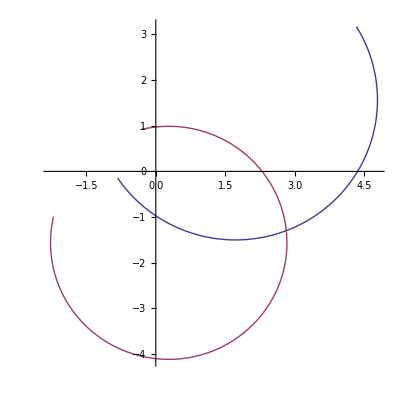

```mathematica
ParametricPlot[{{Re[Q[1,u]],Im[Q[1,u]]},{Re[Q[-1,u]],Im[Q[-1,u]]}},{u,0,1},AspectRatio->1]
```

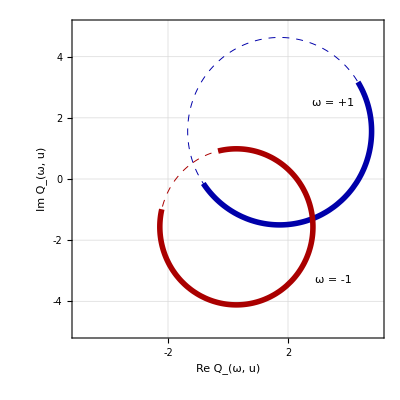

vec4.eps

```mathematica
p1=ParametricPlot[{{Re[Q[1,x^3]],Im[Q[1,x^3]]},{Re[Q[-1,x^3]],Im[Q[-1,x^3]]}},{x,-10,10},PlotRange->{{-5,5},{-5,5}},AspectRatio->1,
ImageSize->{400,400},ImagePadding->{{80,20},{80,20}},
PlotStyle->{{AbsoluteThickness[0.7],Darker[Blue],Dashed},{AbsoluteThickness[0.7],Darker[Red],Dashed},{AbsoluteThickness[0.5],Black}},
BaseStyle->{FontFamily->"Helvetica",14},Frame->True,Axes->False,GridLines->Automatic,
FrameStyle->AbsoluteThickness[0.7],FrameLabel->{Style["Re Q_(ω, u)",14],Style["Im Q_(ω, u)",14]},
Epilog-> {Inset["ω = +1",{3.5,2.5},{Center,Center}],Inset["ω = -1",{3.5,-3.3},{Center,Center}]},
FrameTicks->{LinTicks[-6,6,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-6,6,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-6,6,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[-6,6,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}];
p2=ParametricPlot[{{Re[Q[1,u]],Im[Q[1,u]]},{Re[Q[-1,u]],Im[Q[-1,u]]}},{u,0,1},PlotRange->{{-0.1,2.3},{-1.2,1.2}},AspectRatio->1,Axes->False,
PlotStyle->{{AbsoluteThickness[4],Darker[Blue]},{AbsoluteThickness[4],Darker[Red]}}];
plot1=Show[p1,p2]
Export["vec4.eps",plot1]
```